# Covid-19 Exploration

This notebook contains a basic computational exploration of Covid-19. The topics covered include some properties of the disease, it’s spread and precautionary measures put in place around the world. 
This exploration is mainly based on information and data from Wikipedia, Wikidata and the Wolfram Data Framework.

```mathematica
(* Wolfram Alpha summary of COVID-19 *)
WolframAlpha["Covid-19"]
```

WolframAlphaQueryResults

## Wikipedia

```mathematica
(* search for COVID-19-related articles on Wikipedia *)
Panel/@WikipediaSearch["COVID-19"]
```

{CoViD 19,COVID-19 testing,COVID-19 vaccine,COVID-19 apps,COVID-19 drug development,COVID-19 drug repurposing research,COVID-19 in pregnancy,COVID-19 surveillance,COVID-19 Case-Cluster-Study,COVID-19 Solidarity Response Fund,COVID-19 Congressional Oversight Commission,COVID-19 crisis,COVID-19 in India,COVID-19 in the United States,COVID-19 Hospital,COVID-19 by country,COVID-19 in the UK,COVID-19 outbreak in Italy,COVID-19 in Spain,COVID-19 in Canada,COVID-19 conspiracy,COVID-19 pandemic in mainland China,Covid-19 in Australia,COVID-19 outbreak in Germany,COVID-19 outbreak in Daegu,COVID-19 outbreak in Sweden,COVID-19 in France,COVID-19 in NY,COVID-19 outbreak in South Africa,COVID-19 outbreak in Poland,COVID-19 outbreak in Russia,COVID-19 outbreak in Mexico,Covid-19 virus,COVID-19 in Eire,COVID-19 outbreak in the Philippines,COVID-19 Pandemic Unemployment Payment,COVID-19 in New Zealand,COVID-19 in Europe,COVID-19 in Pakistan,COVID-19 in Bangladesh,COVID-19 outbreak in Brazil,COVID-19 outbreak in Turkey,COVID-19 outbreak in Japan,COVID-19 outbreak in Malaysia,COVID-19 outbreak in the Czech Republic,COVID-19 recession,COVID-19 outbreak in Singapore,COVID-19 outbreak in Indonesia,COVID-19 outbreak in Belgium,COVID-19 outbreak in Greece}

```mathematica
(* summary of Wikipedia article on "CoViD 19" *)
Style[StringReplace[WikipediaData["CoViD 19", "SummaryPlaintext"], ("." ~~ w:LetterCharacter) :> ".\n\n"<>w], "Text", 15]
```

Coronavirus disease 2019 (COVID-19) is an infectious disease caused by severe acute respiratory syndrome coronavirus 2 (SARS-CoV-2). It was first identified in December 2019 in Wuhan, China, and has since spread globally, resulting in an ongoing pandemic. As of 17 May 2020, more than 4.68 million cases have been reported across 188 countries and territories, resulting in more than 313,000 deaths. More than 1.72 million people have recovered.

Common symptoms include fever, cough, fatigue, shortness of breath, and loss of smell and taste. While the majority of cases result in mild symptoms, some progress to an unusual form of acute respiratory distress syndrome (ARDS) likely precipitated by cytokine storm, multi-organ failure, septic shock, and blood clots. The time from exposure to onset of symptoms is typically around five days but may range from two to fourteen days.

The virus is primarily spread between people during close contact, most often via small droplets produced by coughing, sneezing, and talking. The droplets usually fall to the ground or onto surfaces rather than travelling through air over long distances. Less commonly, people may become infected by touching a contaminated surface and then touching their face. It is most contagious during the first three days after the onset of symptoms, although spread is possible before symptoms appear, and from people who do not show symptoms. The standard method of diagnosis is by real-time reverse transcription polymerase chain reaction (rRT-PCR) from a nasopharyngeal swab. Chest CT imaging may also be helpful for diagnosis in individuals where there is a high suspicion of infection based on symptoms and risk factors; however, guidelines do not recommend using CT imaging for routine screening.

Recommended measures to prevent infection include frequent hand washing, maintaining physical distance from others (especially from those with symptoms), quarantine (especially for those with symptoms), covering coughs, and keeping unwashed hands away from the face. In addition, the use of a face covering is recommended for those who suspect they have the virus and their caregivers. Recommendations for face covering use by the general public vary, with some authorities recommending for them, some recommending against them, and others requiring their use. There is limited evidence for or against the use of masks (medical or other) in healthy individuals in the wider community.

According to the World Health Organization, there are no available vaccines nor specific antiviral treatments for COVID-19. On 1 May 2020, the United States gave Emergency Use Authorization to the antiviral remdesivir for people hospitalized with severe COVID‑19. Management involves the treatment of symptoms, supportive care, isolation, and experimental measures. The World Health Organization (WHO) declared the COVID‑19 outbreak a Public Health Emergency of International Concern (PHEIC) on 30 January 2020 and a pandemic on 11 March 2020. Local transmission of the disease has occurred in most countries across all six WHO regions.

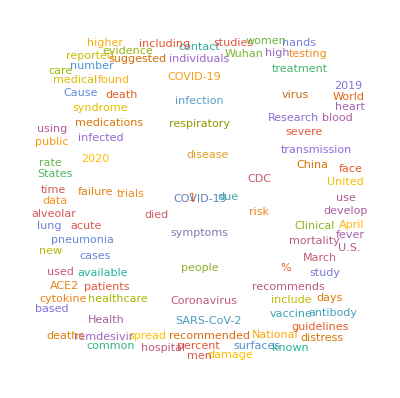

```mathematica
(* wordcloud of the Covid-19 Wikipedia article *)
WordCloud@DeleteStopwords@TextWords@WikipediaData["CoViD 19", "ArticlePlaintext"]
```

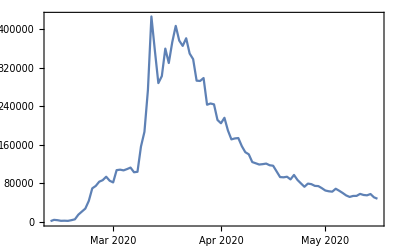

```mathematica
(* daily page hits of the article *)
DateListPlot[WikipediaData["CoViD 19", "DailyPageHits"], PlotTheme->"Detailed"]
```

We can also see a breakdown of how people have been accessing the article. Comparably way fewer people use the Wikipedia mobile app and that’s probably why that line is mostly flat for the entire period. Mobile web and Desktop views were initially the same but mobile grew faster in March. Views from Mobile and Desktop are now similar again in mid-May, though mobile is still slightly above. This could be because people are generally using their phones more frequently than their laptops each day.

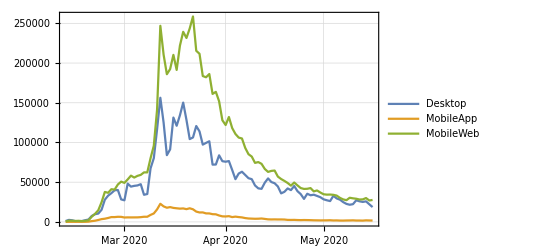

```mathematica
(* breakdown of page views by access types *)
With[{accessData = Association[(# -> WikipediaData["CoViD 19", {"DailyPageHits", "Access" -> #}])&/@{"Desktop", "MobileApp", "MobileWeb"}]},
DateListPlot[accessData, PlotTheme->"Detailed", PlotRange->All]
]
```

But are all of those views even from real people? What portion of them are from bots?

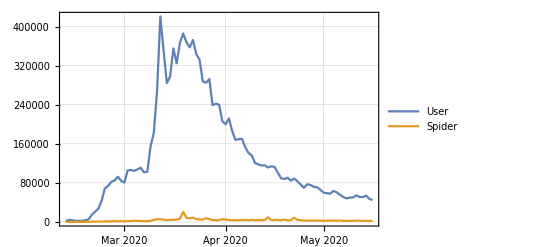

```mathematica
(* "Bot" is currenlty returning an error: "Wikipedia servers are currently under maintenance or experiencing a technical problem. Please try again in a few minutes." *)
With[{agentData = Association[(# -> WikipediaData["CoViD 19", {"DailyPageHits", "Agent" -> #}])&/@{"User", "Spider"(*, "Bot"*)}]},
DateListPlot[agentData, PlotTheme->"Detailed", PlotRange->All]
]
```

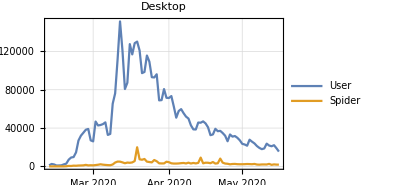
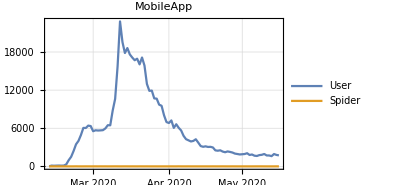
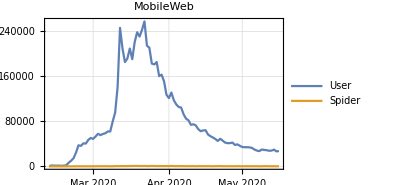
-Graphics- | -Graphics- | -Graphics-

```mathematica
(* Spider views appear to come only from Desktop. Bot data also not available in this case *)
Grid@List@Table[
With[{accessAgentData = Association[#->WikipediaData["CoViD 19", {"DailyPageHits", "Access"->ac, "Agent"->#}]&/@{"User", "Spider"(*, "Bot"*)}]},
DateListPlot[accessAgentData, PlotLabel->ac, PlotTheme->"Detailed", PlotRange->All, ImageSize->300]],
{ac, {"Desktop", "MobileApp", "MobileWeb"}}]
```

## Wikidata

```mathematica
(* search for COVID-19-related data on Wikipedia *)
WikidataSearch["Covid-19"]
```

{ExternalIdentifier[WikidataID,Q84263196,<|Label→COVID-19,Description→zoonotic respiratory syndrome and infectious disease in humans, caused by SARS coronavirus 2|>]WikidataCOVID-19http://www.wikidata.org/entity/Q84263196,ExternalIdentifier[WikidataID,Q87718451,<|Label→2020 COVID-19 pandemic in Nigeria|>]Wikidata2020 COVID-19 pandemic in Nigeriahttp://www.wikidata.org/entity/Q87718451,ExternalIdentifier[WikidataID,Q81068910,<|Label→COVID-19 pandemic,Description→ongoing pandemic of COVID-19|>]WikidataCOVID-19 pandemichttp://www.wikidata.org/entity/Q81068910,ExternalIdentifier[WikidataID,Q93202208,<|Label→COVID-19,Description→scientific article published on 01 April 2020|>]WikidataCOVID-19http://www.wikidata.org/entity/Q93202208,ExternalIdentifier[WikidataID,Q93219706,<|Label→COVID-19,Description→scientific article published on 23 April 2020|>]WikidataCOVID-19http://www.wikidata.org/entity/Q93219706,ExternalIdentifier[WikidataID,Q91601520,<|Label→COVID-19,Description→scientific article published on 30 March 2020|>]WikidataCOVID-19http://www.wikidata.org/entity/Q91601520,ExternalIdentifier[WikidataID,Q94502207,<|Label→Covid-19,Description→scientific article published on 30 April 2020|>]WikidataCovid-19http://www.wikidata.org/entity/Q94502207,ExternalIdentifier[WikidataID,Q84055514,<|Label→2020 COVID-19 pandemic in India,Description→details of ongoing viral pandemic in India in 2020|>]Wikidata2020 COVID-19 pandemic in Indiahttp://www.wikidata.org/entity/Q84055514,ExternalIdentifier[WikidataID,Q83741704,<|Label→COVID-19 pandemic by country and territory,Description→details regarding the 2019–20 coronavirus pandemic by country and territory|>]WikidataCOVID-19 pandemic by country and territoryhttp://www.wikidata.org/entity/Q83741704,ExternalIdentifier[WikidataID,Q83873577,<|Label→COVID-19 pandemic in the United States,Description→ongoing coronavirus pandemic in the United States|>]WikidataCOVID-19 pandemic in the United Stateshttp://www.wikidata.org/entity/Q83873577}

```mathematica
(* view the properties of a given Wikidata item *)
WikidataData[ExternalIdentifier["WikidataID","Q87718451",<|"Label"->"2020 COVID-19 pandemic in Nigeria"|>]"Wikidata""2020 COVID-19 pandemic in Nigeria"http://www.wikidata.org/entity/Q87718451, "NonIdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P17,<|Label→country,Description→sovereign state of this item (not to be used for human beings)|>]Wikidatacountryhttp://www.wikidata.org/entity/P17,ExternalIdentifier[WikidataID,P31,<|Label→instance of,Description→that class of which this subject is a particular example and member|>]Wikidatainstance ofhttp://www.wikidata.org/entity/P31,ExternalIdentifier[WikidataID,P237,<|Label→coat of arms,Description→subject's coat of arms|>]Wikidatacoat of armshttp://www.wikidata.org/entity/P237,ExternalIdentifier[WikidataID,P276,<|Label→location,Description→location of the item, physical object or event is within. In case of an administrative entity use P131. In case of a distinct terrain feature use P706.|>]Wikidatalocationhttp://www.wikidata.org/entity/P276,ExternalIdentifier[WikidataID,P361,<|Label→part of,Description→object of which the subject is a part (if this subject is already part of object A which is a part of object B, then please only make the subject part of object A). Inverse property of "has part" (P527, see also "has parts of the class" (P2670)).|>]Wikidatapart ofhttp://www.wikidata.org/entity/P361,ExternalIdentifier[WikidataID,P580,<|Label→start time,Description→time an item begins to exist or a statement starts being valid|>]Wikidatastart timehttp://www.wikidata.org/entity/P580,ExternalIdentifier[WikidataID,P625,<|Label→coordinate location,Description→geocoordinates of the subject. For Earth, please note that only WGS84 coordinating system is supported at the moment|>]Wikidatacoordinate locationhttp://www.wikidata.org/entity/P625,ExternalIdentifier[WikidataID,P373,<|Label→Commons category,Description→name of the Wikimedia Commons category containing files related to this item (without the prefix "Category:")|>]WikidataCommons categoryhttp://www.wikidata.org/entity/P373,ExternalIdentifier[WikidataID,P828,<|Label→has cause,Description→underlying cause, thing that ultimately resulted in this effect|>]Wikidatahas causehttp://www.wikidata.org/entity/P828,ExternalIdentifier[WikidataID,P910,<|Label→topic's main category,Description→main Wikimedia category|>]Wikidatatopic's main categoryhttp://www.wikidata.org/entity/P910,ExternalIdentifier[WikidataID,P1120,<|Label→number of deaths,Description→Total (cumulative) number of people who died since start as a direct result of an event or cause|>]Wikidatanumber of deathshttp://www.wikidata.org/entity/P1120,ExternalIdentifier[WikidataID,P1603,<|Label→number of cases,Description→cumulative number of confirmed, probable and suspected occurrences|>]Wikidatanumber of caseshttp://www.wikidata.org/entity/P1603,ExternalIdentifier[WikidataID,P1846,<|Label→distribution map,Description→distribution of item on a mapped area (for  range map of taxa, use (P181).)|>]Wikidatadistribution maphttp://www.wikidata.org/entity/P1846,ExternalIdentifier[WikidataID,P2572,<|Label→hashtag,Description→hashtag associated with this entity. Format: do not include the "#" symbol|>]Wikidatahashtaghttp://www.wikidata.org/entity/P2572,ExternalIdentifier[WikidataID,P3457,<|Label→case fatality rate,Description→proportion of patients who die of a particular medical condition out of all who have this condition within a given time frame|>]Wikidatacase fatality ratehttp://www.wikidata.org/entity/P3457,ExternalIdentifier[WikidataID,P8010,<|Label→number of recoveries,Description→number of cases that recovered from disease|>]Wikidatanumber of recoverieshttp://www.wikidata.org/entity/P8010,ExternalIdentifier[WikidataID,P8045,<|Label→organized response related to outbreak,Description→specific action taken or system used as a reaction to an outbreak|>]Wikidataorganized response related to outbreakhttp://www.wikidata.org/entity/P8045}

```mathematica
(* view data and their respective sources *)
Values@WikidataData[ExternalIdentifier["WikidataID","Q87718451",<|"Label"->"2020 COVID-19 pandemic in Nigeria"|>]"Wikidata""2020 COVID-19 pandemic in Nigeria"http://www.wikidata.org/entity/Q87718451, ExternalIdentifier["WikidataID","P1120",<|"Label"->"number of deaths","Description"->"Total (cumulative) number of people who died since start as a direct result of an event or cause"|>]"Wikidata""number of deaths"http://www.wikidata.org/entity/P1120,
Method -> {"StatementFormat" -> {"Association", "IncludeQualifiers"->True, "IncludeReferences"->True}}] // Short[#,5]&
```

{{0.,{Day: Tue 17 Mar 2020},{<|ExternalIdentifier[WikidataID,P585,<|Label→point in time,Description→time and date something took place, existed or a statement was true|>]Wikidatapoint in timehttp://www.wikidata.org/entity/P585→{Day: Mon 16 Mar 2020},ExternalIdentifier[WikidataID,P248,<|Label→stated in,Description→to be used in the references field to refer to the information document or database in which a claim is made; for qualifiers use P805|>]Wikidatastated inhttp://www.wikidata.org/entity/P248→{ExternalIdentifier[WikidataID,Q87779474,<|Label→Novel Coronavirus (2019-nCoV) Situation Report 56,Description→report from the WHO about COVID-19 epidemic at 16 March 2020|>]WikidataNovel Coronavirus (2019-nCoV) Situation Report 56http://www.wikidata.org/entity/Q87779474}|>,<|ExternalIdentifier[WikidataID,P248,<|Label→stated in,Description→to be used in the references field to refer to the information document or database in which a claim is made; for qualifiers use P805|>]Wikidatastated inhttp://www.wikidata.org/entity/P248→{ExternalIdentifier[WikidataID,Q87843252,<|Label→Novel Coronavirus (2019-nCoV) Situation Report 57,Description→report from the WHO about COVID-19 epidemic at 17 March 2020|>]WikidataNovel Coronavirus (2019-nCoV) Situation Report 57http://www.wikidata.org/entity/Q87843252}|>,<|ExternalIdentifier[WikidataID,P143,<|Label→imported from Wikimedia project,Description→source of this claim's value; used in references section by bots importing data from Wikimedia projects; also allowed to be used for manual imports|>]Wikidataimported from Wikimedia projecthttp://www.wikidata.org/entity/P143→{ExternalIdentifier[WikidataID,Q328,<|Label→English Wikipedia,Description→English‑language edition of the free online encyclopedia|>]WikidataEnglish Wikipediahttp://www.wikidata.org/entity/Q328}|>}},{103.,{Day: Wed 6 May 2020},{<|ExternalIdentifier[WikidataID,P813,<|Label→retrieved,Description→date or point in time that information was retrieved from a database or website (for use in online sources)|>]Wikidataretrievedhttp://www.wikidata.org/entity/P813→{Day: Thu 7 May 2020},ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://github.com/datasets/covid-19]}|>}},{143.,{Day: Sun 10 May 2020},{<|ExternalIdentifier[WikidataID,P813,<|Label→retrieved,Description→date or point in time that information was retrieved from a database or website (for use in online sources)|>]Wikidataretrievedhttp://www.wikidata.org/entity/P813→{Day: Tue 12 May 2020},ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://datahub.io/core/covid-19]},ExternalIdentifier[WikidataID,P7793,<|Label→filename in archive,Description→qualifier and referencing property to identify the specific file within a compressed archive that is relevant to a statement|>]Wikidatafilename in archivehttp://www.wikidata.org/entity/P7793→{r/countries-aggregated.csv}|>}},{158.,{Day: Tue 12 May 2020},{<|ExternalIdentifier[WikidataID,P813,<|Label→retrieved,Description→date or point in time that information was retrieved from a database or website (for use in online sources)|>]Wikidataretrievedhttp://www.wikidata.org/entity/P813→{Day: Thu 14 May 2020},ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://datahub.io/core/covid-19]},ExternalIdentifier[WikidataID,P7793,<|Label→filename in archive,Description→qualifier and referencing property to identify the specific file within a compressed archive that is relevant to a statement|>]Wikidatafilename in archivehttp://www.wikidata.org/entity/P7793→{r/countries-aggregated.csv}|>}},{1.,{Day: Sat 28 Mar 2020}},«21»,{68.,{Day: Fri 1 May 2020},{<|ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://ncdc.gov.ng/diseases/sitreps/?cat=14&name=An%20update%20of%20COVID-19%20outbreak%20in%20Nigeria]}|>}},{85.,{Day: Sat 2 May 2020},{<|ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://ncdc.gov.ng/diseases/sitreps/?cat=14&name=An%20update%20of%20COVID-19%20outbreak%20in%20Nigeria]}|>}},{87.,{Day: Sun 3 May 2020},{<|ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://ncdc.gov.ng/diseases/sitreps/?cat=14&name=An%20update%20of%20COVID-19%20outbreak%20in%20Nigeria]}|>}},{93.,{Day: Mon 4 May 2020},{<|ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://ncdc.gov.ng/diseases/sitreps/?cat=14&name=An%20update%20of%20COVID-19%20outbreak%20in%20Nigeria]}|>}}}

```mathematica
(* get data for no. of cases and deaths *)
casesAndDeathsInNigeria = Association[
# -> WikidataData[ExternalIdentifier["WikidataID","Q87718451",<|"Label"->"2020 COVID-19 pandemic in Nigeria"|>]"Wikidata""2020 COVID-19 pandemic in Nigeria"http://www.wikidata.org/entity/Q87718451, #,
Method -> {"StatementFormat" -> {"Association", "IncludeQualifiers"->True, "IncludeReferences"->False}}]&/@{ExternalIdentifier["WikidataID","P1603",<|"Label"->"number of cases","Description"->"cumulative number of confirmed, probable and suspected occurrences"|>]"Wikidata""number of cases"http://www.wikidata.org/entity/P1603,  ExternalIdentifier["WikidataID","P1120",<|"Label"->"number of deaths","Description"->"Total (cumulative) number of people who died since start as a direct result of an event or cause"|>]"Wikidata""number of deaths"http://www.wikidata.org/entity/P1120}
]/.(a_Association /; Length[a]<2) -> Nothing;
```

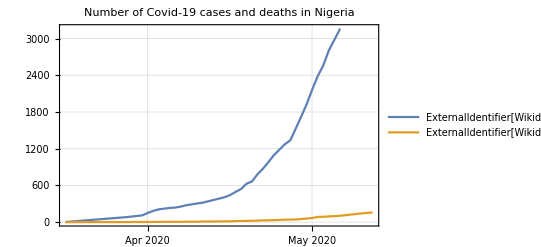

```mathematica
(* plot data *)
DateListPlot[MapAt[Reverse[Flatten@#]&, Values/@casesAndDeathsInNigeria, {;;, ;;}],
PlotTheme->"Detailed", PlotLabel->"Number of Covid-19 cases and deaths in Nigeria"]
```

```mathematica
(* with Wikidata, properties have properties too. this is great for building a custom knowledge graph for a given topic *)
WikidataData[ExternalIdentifier["WikidataID","P1603",<|"Label"->"number of cases","Description"->"cumulative number of confirmed, probable and suspected occurrences"|>]"Wikidata""number of cases"http://www.wikidata.org/entity/P1603, "NonIdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P1629,<|Label→subject item of this property,Description→relationship represented by the property|>]Wikidatasubject item of this propertyhttp://www.wikidata.org/entity/P1629,ExternalIdentifier[WikidataID,P31,<|Label→instance of,Description→that class of which this subject is a particular example and member|>]Wikidatainstance ofhttp://www.wikidata.org/entity/P31,ExternalIdentifier[WikidataID,P1659,<|Label→see also,Description→used to indicate another property that might provide additional information about the Wikidata-property|>]Wikidatasee alsohttp://www.wikidata.org/entity/P1659,ExternalIdentifier[WikidataID,P1855,<|Label→Wikidata property example,Description→example where this Wikidata property is used; target item is one that would use this property, with qualifier the property being described given the associated value|>]WikidataWikidata property examplehttp://www.wikidata.org/entity/P1855,ExternalIdentifier[WikidataID,P2302,<|Label→property constraint,Description→constraint applicable to this Wikidata property|>]Wikidataproperty constrainthttp://www.wikidata.org/entity/P2302,ExternalIdentifier[WikidataID,P2875,<|Label→property usage tracking category,Description→category tracking a Wikidata property in sister projects|>]Wikidataproperty usage tracking categoryhttp://www.wikidata.org/entity/P2875,ExternalIdentifier[WikidataID,P3254,<|Label→property proposal discussion,Description→URL of the page (or page section) on which the creation of the property was discussed|>]Wikidataproperty proposal discussionhttp://www.wikidata.org/entity/P3254}

```mathematica
(* example property of a property *)
WikidataData[ExternalIdentifier["WikidataID","P1603",<|"Label"->"number of cases","Description"->"cumulative number of confirmed, probable and suspected occurrences"|>]"Wikidata""number of cases"http://www.wikidata.org/entity/P1603, ExternalIdentifier["WikidataID","P1659",<|"Label"->"see also","Description"->"used to indicate another property that might provide additional information about the Wikidata-property"|>]"Wikidata""see also"http://www.wikidata.org/entity/P1659]
```

{ExternalIdentifier[WikidataID,P8049,<|Label→number of hospitalized cases,Description→number of cases that are hospitalized|>]Wikidatanumber of hospitalized caseshttp://www.wikidata.org/entity/P8049,ExternalIdentifier[WikidataID,P8204,<|Label→tabular case data,Description→tabular data on Wikimedia Commons of confirmed cases, recoveries, deaths, etc. due to a medical event; corresponds to P8011, P1603, P8049, P8010, P1120. Do not delete such statements.|>]Wikidatatabular case datahttp://www.wikidata.org/entity/P8204,ExternalIdentifier[WikidataID,P1120,<|Label→number of deaths,Description→Total (cumulative) number of people who died since start as a direct result of an event or cause|>]Wikidatanumber of deathshttp://www.wikidata.org/entity/P1120,ExternalIdentifier[WikidataID,P1193,<|Label→prevalence,Description→portion of a population with a given disease|>]Wikidataprevalencehttp://www.wikidata.org/entity/P1193,ExternalIdentifier[WikidataID,P2844,<|Label→incidence,Description→probability of occurrence of a given condition in a population within a specified period of time|>]Wikidataincidencehttp://www.wikidata.org/entity/P2844,ExternalIdentifier[WikidataID,P8011,<|Label→number of clinical tests,Description→cumulative number of clinical tests|>]Wikidatanumber of clinical testshttp://www.wikidata.org/entity/P8011,ExternalIdentifier[WikidataID,P8010,<|Label→number of recoveries,Description→number of cases that recovered from disease|>]Wikidatanumber of recoverieshttp://www.wikidata.org/entity/P8010}

```mathematica
(* see info on a given data collection. this shows the braoder context of the data - it could be subset of a bigger dataset, and/or have it's own parts. *)
WikidataData[ExternalIdentifier["WikidataID","Q83873577",<|"Label"->"2020 COVID-19 pandemic in the United States","Description"->"viral outbreak in the United States"|>]"Wikidata""2020 COVID-19 pandemic in the United States"http://www.wikidata.org/entity/Q83873577, "Dataset"]
```

```mathematica
(* list of countries for which there is Wikidata coverage on Covid-19 pandemic *)
covidPandemicCountries = WikidataData[ExternalIdentifier["WikidataID","Q83741704",<|"Label"->"COVID-19 pandemic by country and territory","Description"->"details regarding the 2019–20 coronavirus pandemic by country and territory"|>]"Wikidata""COVID-19 pandemic by country and territory"http://www.wikidata.org/entity/Q83741704, ExternalIdentifier["WikidataID","P527",<|"Label"->"has part","Description"->"part of this subject; inverse property of \"part of\" (P361). See also \"has parts of the class\" (P2670)."|>]"Wikidata""has part"http://www.wikidata.org/entity/P527];
{Highlighted@Length@covidPandemicCountries, Short[covidPandemicCountries, .2]}
```

{196,{ExternalIdentifier[WikidataID,Q83872271,<|Label→2019–20 coronavirus pandemic in mainland China,Description→viral outbreak in mainland China|>]Wikidata2019–20 coronavirus pandemic in mainland Chinahttp://www.wikidata.org/entity/Q83872271,ExternalIdentifier[WikidataID,Q83872291,<|Label→COVID-19 pandemic in Japan,Description→viral outbreak in Japan|>]WikidataCOVID-19 pandemic in Japanhttp://www.wikidata.org/entity/Q83872291,ExternalIdentifier[WikidataID,Q83872398,<|Label→2019–20 COVID-19 outbreak in South Korea,Description→viral outbreak in South Korea|>]Wikidata2019–20 COVID-19 outbreak in South Koreahttp://www.wikidata.org/entity/Q83872398,ExternalIdentifier[WikidataID,Q83873057,<|Label→COVID-19 pandemic in Vietnam,Description→viral outbreak in Vietnam|>]WikidataCOVID-19 pandemic in Vietnamhttp://www.wikidata.org/entity/Q83873057,ExternalIdentifier[WikidataID,Q83873387,<|Label→2020 COVID-19 pandemic in Singapore,Description→details of ongoing viral outbreak in Singapore|>]Wikidata2020 COVID-19 pandemic in Singaporehttp://www.wikidata.org/entity/Q83873387,ExternalIdentifier[WikidataID,Q83873548,<|Label→2020 COVID-19 pandemic in Australia,Description→viral outbreak in Australia|>]Wikidata2020 COVID-19 pandemic in Australiahttp://www.wikidata.org/entity/Q83873548,ExternalIdentifier[WikidataID,Q83873556,<|Label→2020 COVID-19 pandemic in Malaysia,Description→viral outbreak in Malaysia|>]Wikidata2020 COVID-19 pandemic in Malaysiahttp://www.wikidata.org/entity/Q83873556,ExternalIdentifier[WikidataID,Q83873566,<|Label→2020 COVID-19 pandemic in Thailand,Description→viral outbreak in Thailand|>]Wikidata2020 COVID-19 pandemic in Thailandhttp://www.wikidata.org/entity/Q83873566,ExternalIdentifier[WikidataID,Q83873573,<|Label→2019–20 coronavirus outbreak in Nepal,Description→viral outbreak in Nepal|>]Wikidata2019–20 coronavirus outbreak in Nepalhttp://www.wikidata.org/entity/Q83873573,«178»,ExternalIdentifier[WikidataID,Q87709900,<|Label→2020 COVID-19 pandemic in Mauritania,Description→details of ongoing viral pandemic in Mauritania|>]Wikidata2020 COVID-19 pandemic in Mauritaniahttp://www.wikidata.org/entity/Q87709900,ExternalIdentifier[WikidataID,Q87709973,<|Label→2020 COVID-19 pandemic in Eswatini,Description→viral pandemic in Eswatini|>]Wikidata2020 COVID-19 pandemic in Eswatinihttp://www.wikidata.org/entity/Q87709973,ExternalIdentifier[WikidataID,Q87714704,<|Label→2020 COVID-19 pandemic in Rwanda,Description→viral pandemic in Rwanda|>]Wikidata2020 COVID-19 pandemic in Rwandahttp://www.wikidata.org/entity/Q87714704,ExternalIdentifier[WikidataID,Q87715166,<|Label→2020 COVID-19 pandemic in Bhutan,Description→viral pandemic in Bhutan|>]Wikidata2020 COVID-19 pandemic in Bhutanhttp://www.wikidata.org/entity/Q87715166,ExternalIdentifier[WikidataID,Q87715843,<|Label→2020 COVID-19 pandemic in Andorra,Description→details of ongoing viral pandemic in Teil der COVID-19-Pandemie|>]Wikidata2020 COVID-19 pandemic in Andorrahttp://www.wikidata.org/entity/Q87715843,ExternalIdentifier[WikidataID,Q87722485,<|Label→2020 COVID-19 pandemic in Azerbaijan,Description→viral pandemic in Azerbaijan|>]Wikidata2020 COVID-19 pandemic in Azerbaijanhttp://www.wikidata.org/entity/Q87722485,ExternalIdentifier[WikidataID,Q87729500,<|Label→2020 COVID-19 pandemic in Seychelles,Description→viral pandemic in Seychelles|>]Wikidata2020 COVID-19 pandemic in Seychelleshttp://www.wikidata.org/entity/Q87729500,ExternalIdentifier[WikidataID,Q87729501,<|Label→2020 COVID-19 pandemic in Namibia,Description→viral pandemic in Namibia|>]Wikidata2020 COVID-19 pandemic in Namibiahttp://www.wikidata.org/entity/Q87729501,ExternalIdentifier[WikidataID,Q87733671,<|Label→2020 COVID-19 pandemic in Qatar,Description→viral pandemic in Qatar|>]Wikidata2020 COVID-19 pandemic in Qatarhttp://www.wikidata.org/entity/Q87733671}}

Responses to the outbreak differ from one country to another. Also, the absence of data for a particular country does not suggest that no precautions were put in place.

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q87186365",<|"Label"->"2020 COVID-19 pandemic in the Republic of Ireland","Description"->"details of ongoing viral outbreak in the Republic of Ireland"|>]"Wikidata""2020 COVID-19 pandemic in the Republic of Ireland"http://www.wikidata.org/entity/Q87186365,  ExternalIdentifier["WikidataID","P8045",<|"Label"->"organized response related to outbreak","Description"->"specific action taken or system used as a reaction to an outbreak"|>]"Wikidata""organized response related to outbreak"http://www.wikidata.org/entity/P8045]
```

{ExternalIdentifier[WikidataID,Q93623431,<|Label→2020 Ireland COVID-19 social distancing,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 social distancinghttp://www.wikidata.org/entity/Q93623431,ExternalIdentifier[WikidataID,Q93623429,<|Label→2020 Ireland COVID-19 closing of educational institutions,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 closing of educational institutionshttp://www.wikidata.org/entity/Q93623429,ExternalIdentifier[WikidataID,Q93623435,<|Label→2020 Ireland COVID-19 closing of non-essential businesses,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 closing of non-essential businesseshttp://www.wikidata.org/entity/Q93623435,ExternalIdentifier[WikidataID,Q93623433,<|Label→2020 Ireland COVID-19 lockdown,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 lockdownhttp://www.wikidata.org/entity/Q93623433}

```mathematica
(* see when a particular measure was announced and enacted *)
WikidataData[ExternalIdentifier["WikidataID","Q93623431",<|"Label"->"2020 Ireland COVID-19 social distancing","Description"->"COVID-19 countermeasure in Ireland"|>]"Wikidata""2020 Ireland COVID-19 social distancing"http://www.wikidata.org/entity/Q93623431, "Dataset"]
```

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q93623431",<|"Label"->"2020 Ireland COVID-19 social distancing","Description"->"COVID-19 countermeasure in Ireland"|>]"Wikidata""2020 Ireland COVID-19 social distancing"http://www.wikidata.org/entity/Q93623431, "NonIdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P31,<|Label→instance of,Description→that class of which this subject is a particular example and member|>]Wikidatainstance ofhttp://www.wikidata.org/entity/P31,ExternalIdentifier[WikidataID,P6949,<|Label→announcement date,Description→time of the first public presentation of a subject by the creator, of information by the media|>]Wikidataannouncement datehttp://www.wikidata.org/entity/P6949,ExternalIdentifier[WikidataID,P580,<|Label→start time,Description→time an item begins to exist or a statement starts being valid|>]Wikidatastart timehttp://www.wikidata.org/entity/P580,ExternalIdentifier[WikidataID,P828,<|Label→has cause,Description→underlying cause, thing that ultimately resulted in this effect|>]Wikidatahas causehttp://www.wikidata.org/entity/P828,ExternalIdentifier[WikidataID,P1001,<|Label→applies to jurisdiction,Description→the item (an institution, law, public office ...) or statement belongs to or has power over or applies to the value (a territorial jurisdiction: a country, state, municipality, ...)|>]Wikidataapplies to jurisdictionhttp://www.wikidata.org/entity/P1001}

```mathematica
(* responses of countries for which this data is available *)
covidPandemicResponses = DeleteCases[
Thread[# -> WikidataData[#, ExternalIdentifier["WikidataID","P8045",<|"Label"->"organized response related to outbreak","Description"->"specific action taken or system used as a reaction to an outbreak"|>]"Wikidata""organized response related to outbreak"http://www.wikidata.org/entity/P8045]]&@covidPandemicCountries // Association,
{}];
```

```mathematica
(* Sweden has so far has the highest number of distinct responses, followed by Jordan and New Zealand. *)
ReverseSortBy[Length]@covidPandemicResponses // Dataset[#, MaxItems->5]&
(* Sweden's responses *)
%[1]
```

```mathematica
(* response type and start date data for all countries *)
covidPandemicResponsesData = MapAt[Flatten, WikidataData[#, {ExternalIdentifier["WikidataID","P31",<|"Label"->"instance of","Description"->"that class of which this subject is a particular example and member"|>]"Wikidata""instance of"http://www.wikidata.org/entity/P31, ExternalIdentifier["WikidataID","P580",<|"Label"->"start time","Description"->"time an item begins to exist or a statement starts being valid"|>]"Wikidata""start time"http://www.wikidata.org/entity/P580}]&/@covidPandemicResponses, {;;, ;;}];
(* view data *)
covidPandemicResponsesData // Dataset[#, MaxItems->5]&
```

```mathematica
(* tally of responses by all countries *)
ReverseSortBy[Last]@Tally@Cases[Flatten@Values@covidPandemicResponsesData,_ExternalIdentifier] // Grid[#, Alignment->Right]&
```

ExternalIdentifier[WikidataID,Q88323877,<|Label→closing of educational institutions,Description→action to reduce virus transmission|>]Wikidataclosing of educational institutionshttp://www.wikidata.org/entity/Q88323877 | 56
ExternalIdentifier[WikidataID,Q30314010,<|Label→social distancing,Description→reduction of human social interaction in an effort to prevent the spread of infectious disease|>]Wikidatasocial distancinghttp://www.wikidata.org/entity/Q30314010 | 54
ExternalIdentifier[WikidataID,Q87745167,<|Label→travel restriction,Description→policy|>]Wikidatatravel restrictionhttp://www.wikidata.org/entity/Q87745167 | 50
ExternalIdentifier[WikidataID,Q7257745,<|Label→declaration of public health emergency,Description→The declaration of a public health emergency in response to a (public) health crisis.|>]Wikidatadeclaration of public health emergencyhttp://www.wikidata.org/entity/Q7257745 | 44
ExternalIdentifier[WikidataID,Q88761394,<|Label→travel ban,Description→restriction of all means of travel|>]Wikidatatravel banhttp://www.wikidata.org/entity/Q88761394 | 38
ExternalIdentifier[WikidataID,Q88761692,<|Label→flight ban,Description→Restriction of air travel, e.g. closure of airports|>]Wikidataflight banhttp://www.wikidata.org/entity/Q88761692 | 32
ExternalIdentifier[WikidataID,Q6665312,<|Label→lockdown,Description→emergency protocol that prevents people or information from leaving an area|>]Wikidatalockdownhttp://www.wikidata.org/entity/Q6665312 | 31
ExternalIdentifier[WikidataID,Q223625,<|Label→curfew,Description→political or police ban on entering public areas such as streets or squares|>]Wikidatacurfewhttp://www.wikidata.org/entity/Q223625 | 28
ExternalIdentifier[WikidataID,Q89681240,<|Label→closing of non-essential businesses|>]Wikidataclosing of non-essential businesseshttp://www.wikidata.org/entity/Q89681240 | 16
ExternalIdentifier[WikidataID,Q89211965,<|Label→decision by the Swedish Government,Description→formal decisions in government meetings|>]Wikidatadecision by the Swedish Governmenthttp://www.wikidata.org/entity/Q89211965 | 5
ExternalIdentifier[WikidataID,Q88307738,<|Label→stay-at-home order,Description→type of quarantine|>]Wikidatastay-at-home orderhttp://www.wikidata.org/entity/Q88307738 | 3
ExternalIdentifier[WikidataID,Q182899,<|Label→quarantine,Description→epidemiological intervention of restriction on the movement of people and goods, which is intended to prevent the spread of infectious disease or pests|>]Wikidataquarantinehttp://www.wikidata.org/entity/Q182899 | 3
ExternalIdentifier[WikidataID,Q5370734,<|Label→emergency procedure,Description→plan of action to deal with an emergency|>]Wikidataemergency procedurehttp://www.wikidata.org/entity/Q5370734 | 2
ExternalIdentifier[WikidataID,Q88707306,<|Label→border closure,Description→action to reduce virus transmission in the community|>]Wikidataborder closurehttp://www.wikidata.org/entity/Q88707306 | 1
ExternalIdentifier[WikidataID,Q88705465,<|Label→travel advice as non-pharmaceutical countermeasure,Description→action to reduce virus transmission in the community|>]Wikidatatravel advice as non-pharmaceutical countermeasurehttp://www.wikidata.org/entity/Q88705465 | 1
ExternalIdentifier[WikidataID,Q88324058,<|Label→avoiding crowding,Description→action to reduce virus transmission|>]Wikidataavoiding crowdinghttp://www.wikidata.org/entity/Q88324058 | 1
ExternalIdentifier[WikidataID,Q820655,<|Label→legislative act,Description→formal written document that creates law, including acts, executive orders, and by-laws|>]Wikidatalegislative acthttp://www.wikidata.org/entity/Q820655 | 1
ExternalIdentifier[WikidataID,Q428148,<|Label→regulation,Description→general term for rules or controls, including delegated legislation and self-regulation|>]Wikidataregulationhttp://www.wikidata.org/entity/Q428148 | 1
ExternalIdentifier[WikidataID,Q2795484,<|Label→implementing regulation,Description→regulation on the details of the implementation of a law|>]Wikidataimplementing regulationhttp://www.wikidata.org/entity/Q2795484 | 1
ExternalIdentifier[WikidataID,Q207184,<|Label→press release,Description→instrument of public relations|>]Wikidatapress releasehttp://www.wikidata.org/entity/Q207184 | 1
ExternalIdentifier[WikidataID,Q1864008,<|Label→legal act,Description→juridical fact in which the subject who made it happen acted under free will|>]Wikidatalegal acthttp://www.wikidata.org/entity/Q1864008 | 1
ExternalIdentifier[WikidataID,Q1032176,<|Label→countermeasure,Description→specific action taken or system used to offset another action|>]Wikidatacountermeasurehttp://www.wikidata.org/entity/Q1032176 | 1

```mathematica
(* compare start dates of Covid-19 responses around the world *)
responseTimelinePlot[response_, plotLabel_] := Block[{pos,data},
pos = Position[covidPandemicResponsesData, {response,_}];
data = KeyMap[Capitalize@StringDelete[#@"Label", __~~"in "]&, Association@Thread[pos⟦;;, 1, 1⟧ -> Extract[covidPandemicResponsesData, pos]⟦;;, 2⟧]];
TimelinePlot[Association@data, PlotLayout->"VerticalGrouped", PlotTheme->"Business", AspectRatio->.4, ImageSize->{Automatic, 500}, PlotLabel->plotLabel]
]
```

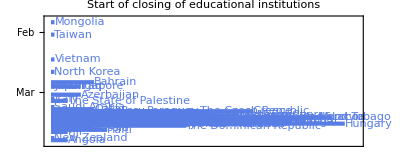

```mathematica
(* educational institutions *)
responseTimelinePlot[ExternalIdentifier["WikidataID","Q88323877",<|"Label"->"closing of educational institutions","Description"->"action to reduce virus transmission"|>]"Wikidata""closing of educational institutions"http://www.wikidata.org/entity/Q88323877, "Start of closing of educational institutions"]
```

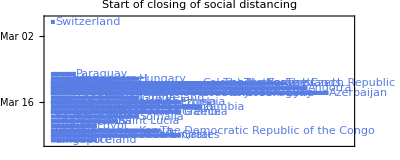

```mathematica
(* social distancing *)
responseTimelinePlot[ExternalIdentifier["WikidataID","Q30314010",<|"Label"->"social distancing","Description"->"reduction of human social interaction in an effort to prevent the spread of infectious disease"|>]"Wikidata""social distancing"http://www.wikidata.org/entity/Q30314010, "Start of closing of social distancing"]
```

Note the not every country is included in the couple of plots above. For example, social distancing was introduced in the UK in March but this does not appear in Wikidata.

### Government measures data from Wolfram Data Repository

On the Wolfram Data Repository, there is a dataset on measures taken by governments around the world. This dataset contains more detailed information than what we can pull from Wikidata.

-Graphics-

```mathematica
(* resource object *)
resObj = ResourceObject["Coronavirus COVID-19 Pandemic Government Measures"]
```

ResourceObject[…]

```mathematica
(* get resource data *)
resObjData = ResourceData@resObj
```

Dataset[<>]

Each enacted measure is categorised and contains 18 a total of properties including its implementation data and the source of the information.

```mathematica
resObjData[GroupBy@"Category", ;;, "Measure"][;;, Tally][;;, ReverseSortBy[Last]]
```

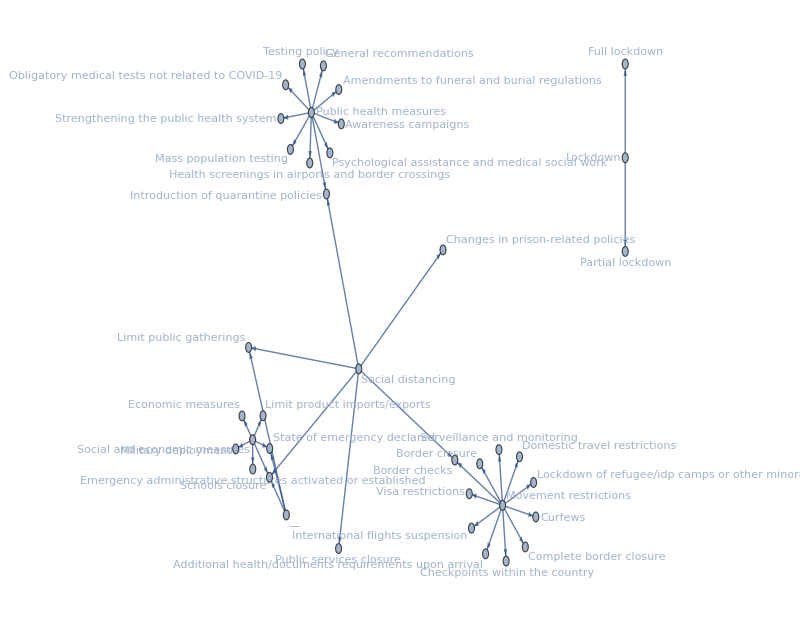

```mathematica
(* groupings of categories and measures *)
GraphPlot[Flatten[Thread/@(Normal@Normal@resObjData[GroupBy@"Category", ;;, "Measure"][;;, DeleteDuplicates])], 
VertexLabels->"Name", GraphLayout->"BalloonEmbedding", ImageSize->800, DirectedEdges->True, AspectRatio->Automatic
]
```

```mathematica
(* category-measure tally data *)
cmTallies = Normal@Echo[Tally/@resObjData[GroupBy@"Category", ;;, "Measure"]];
```

```mathematica
(* breakdown of categories and measures *)
Table[
With[{cat = cmTallies⟦i⟧},
PieChart[Association[Rule@@@cat],
ChartLabels->Callout@Automatic, PlotRange->Full, ImageSize->{Automatic, 200}, PlotLabel->Keys[cmTallies]⟦i⟧]
], {i, Range@Length@cmTallies}] // 
Multicolumn[#, 2, ItemSize->Full, Alignment->Center, Frame->All, FrameStyle->LightGray]&
```

-Graphics-

```mathematica
(* proportions of measures - applied as graph edge thickness values below *)
measuresEdgeSizes = Table[
Block[{cat = Take[cmTallies, {i}], vals, sum},
vals = First@Values@cat;
sum = Total@vals⟦;;, 2⟧;
vals/.{meas_String, no_Integer} :> Rule[Keys[cat]⟦1⟧, meas] -> no],
{i, Range@Length@cmTallies}] // Flatten;

measuresEdgeSizes = Thread[measuresEdgeSizes⟦;;, 1⟧ -> (Directive[{Thickness[0.01*#], Opacity@#}] &/@ (.2 + Rescale@measuresEdgeSizes⟦;;, 2⟧))];
```

```mathematica
(* proportions of categories - applied as vertex size values below *)
categoriesVertexSizes = Join[
N[#/1000] &/@ Total/@MapAt[Last, cmTallies, {;;, ;;}] // Normal,
Thread[measuresEdgeSizes⟦;;, 1, 2⟧ -> 0.3]
];
```

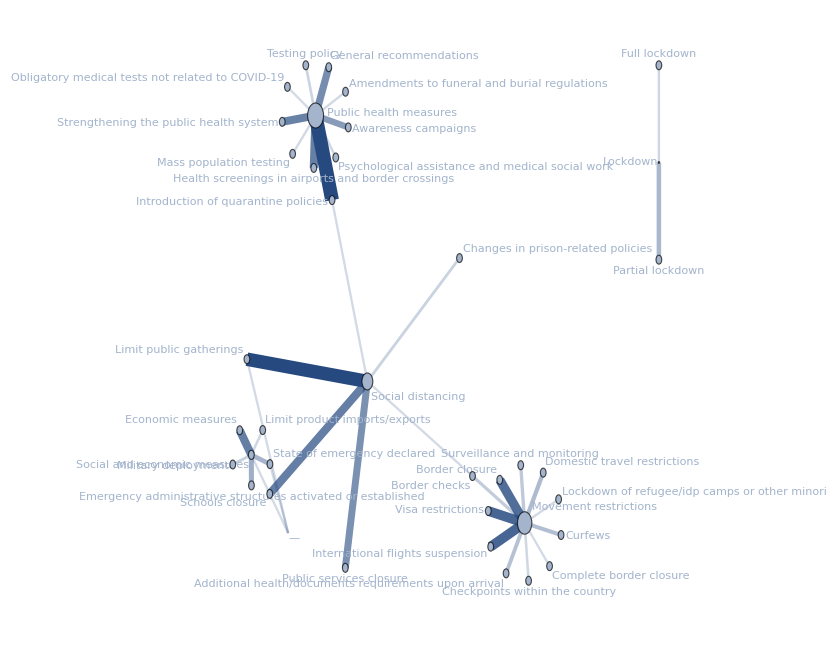

```mathematica
(* graphical form of breakdown *)
Graph[measuresEdgeSizes⟦;;, 1⟧,
EdgeStyle->measuresEdgeSizes, VertexLabels->"Name", DirectedEdges->False, GraphLayout->"BalloonEmbedding", VertexSize->categoriesVertexSizes]
```

## Wolfram Data Framework / Entities

Natural language input “Covid-19” is automatically interpreted as a disease and converted to an explorable real-world entity.

WolframAlphaQueryParseResults

COVID-19

```mathematica
(* Covid-19 as a disease entity *)
covid19 = Entity["Disease","NovelCoronavirusDisease"]; covid19["Properties"]
```

{average patient age,age of onset,associated genes,basic reproduction number,average patient BMI,average temperature,causes,common symptoms,definition,average diastolic blood pressure,duration,entity classes,exposure to disease onset,average patient height,ICD-9 code,ICD-10 code,image,name,prevalence,prevalence rate,prevention,risks,medical specialty,average systolic blood pressure,transmission,treatment,average patient weight}

```mathematica
(* properties of Covid-19 *)
covid19["Dataset"]
```

```mathematica
(* see how Covid-19 compares to other infectious diseases *)
infectDis = EntityList@FilteredEntityClass["Disease", EntityFunction[dis, MemberQ[dis@"Specialty", "infectious disease"]]]
```

{Ebola virus disease,cholera,salmonella infections,shigellosis,botulism,intestinal infection due to Clostridium difficile,infectious colitis, enteritis, and gastroenteritis,infectious diarrhea,tuberculosis,leprosy,diphtheria,whooping cough,streptococcal sore throat and scarlet fever,streptococcal sore throat,tetanus,toxic shock syndrome,Helicobacter pylori infection of an unspecified site,smallpox,chicken pox,herpes simplex,genital herpes,herpes simplex without complications,measles,rubella,yellow fever,Dengue fever,eastern equine encephalitis,viral hepatitis,viral hepatitis B without hepatic coma,unspecified viral hepatitis C,rabies,mumps,hand, foot, and mouth disease,infectious mononucleosis,Condyloma acuminatum,unclassified diseases due to viruses and Chlamydiae,severe acute respiratory syndrome,unspecified type of chlamydial infection co-occurring with other medical conditions,rickettsioses,malaria,lyme disease,syphilis,gonococcal infections,unspecified type of venereal disease,pinta,dermatophytosis of the foot,schistosomiasis,cysticercosis,trichinosis,enterobiasis,lice infestation,scabies,neutropenia,meningitis due to an unspecified cause,acute and subacute endocarditis,common cold,acute pharyngitis,acute bronchitis,chronic tonsillitis,Legionnaires' disease,bronchopneumonia,influenza,urinary tract infection of an unspecified site,orchitis and epididymitis,vascular disorders of the male genital organs,vaginitis and vulvovaginitis,cellulitis and abscess of an unspecified digit,impetigo,pityriasis rosea,necrotizing fasciitis,osteomyelitis, periostitis, and other infections involving bone,neonatal candida infection,sepsis,Middle East respiratory syndrome,COVID-19,Zika virus disease}

```mathematica
(* prevention measures *)
infectDisPrevention = DeleteMissing@ParallelMap[(# -> #[EntityProperty["Disease","Prevention"]])&, infectDis];
Short[%]
```

{Ebola virus disease→{coordinated medical services,careful handling of bushmeat},«50»,Zika virus disease→{decreasing mosquito bites,condoms}}

```mathematica
(* groupings of infectious diseases by prevention measures *)
Keys/@GroupBy[infectDisPrevention, Last] // KeySort // Dataset
```

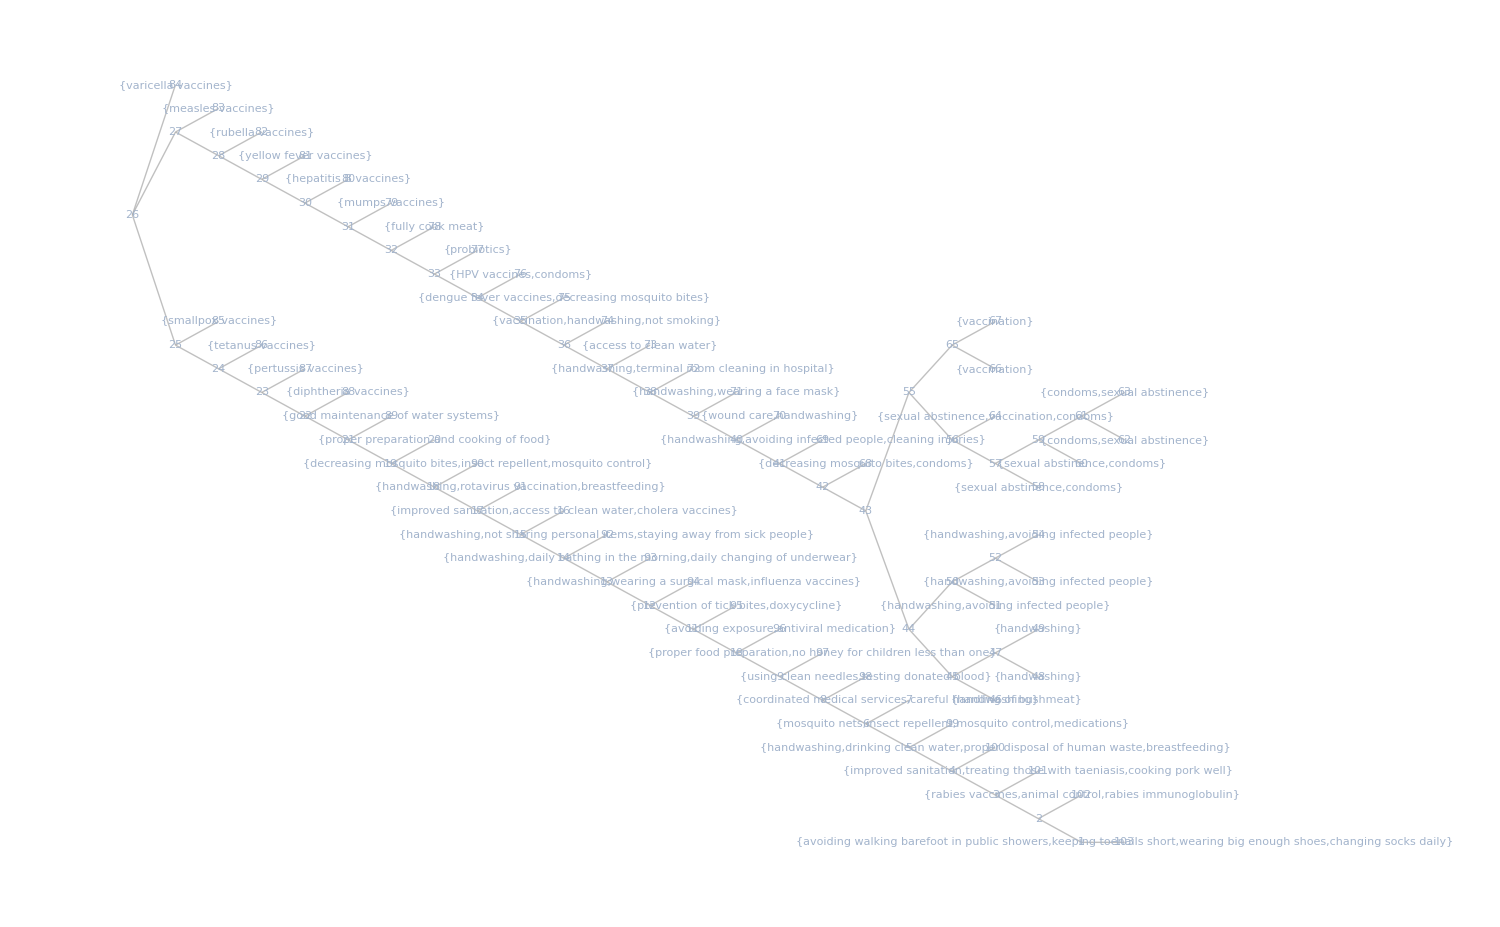

```mathematica
(* similarity between prevention measures *)
Magnify[ClusteringTree[
Values@infectDisPrevention, VertexShapeFunction->"Name", GraphLayout->{"LayeredEmbedding", "Orientation"->Left, "LeafDistance"->1, LayerSizeFunction->(1&)}, 
ImageSize->1500, AspectRatio->1/GoldenRatio], .8]
```

```mathematica
(* exposure to onset. note that data is not available for some entities  *)
infectDisExp = DeleteMissing@ParallelMap[(# -> #[EntityProperty["Disease","ExposureToDiseaseOnset"]])&, infectDis]
```

{Ebola virus disease→(2to21) days,cholera→(1/12 to5) days,salmonella infections→(1/2 to3) days,shigellosis→(1to2) days,botulism→(1/2 to3) days,diphtheria→(2to5) days,streptococcal sore throat→(1to3) days,tetanus→(3to21) days,smallpox→(7to21) days,chicken pox→(10to21) days,genital herpes→(2to12) days,measles→(8to12) days,rubella→14. days,yellow fever→(3to6) days,Dengue fever→(3to14) days,eastern equine encephalitis→(4to10) days,viral hepatitis B without hepatic coma→(72/73 to 432/73) mo,mumps→(14to21) days,hand, foot, and mouth disease→(3to6) days,Condyloma acuminatum→(1to8) mo,unclassified diseases due to viruses and Chlamydiae→(7to21) days,severe acute respiratory syndrome→(2to7) days,unspecified type of chlamydial infection co-occurring with other medical conditions→(14to21) days,rickettsioses→(7to14) days,malaria→(10to15) days,lyme disease→7. days,enterobiasis→(4to8) wk,scabies→(2to6) wk,Legionnaires' disease→(2to10) days,influenza→3. days,Middle East respiratory syndrome→(2to14) days,COVID-19→(2to14) days}

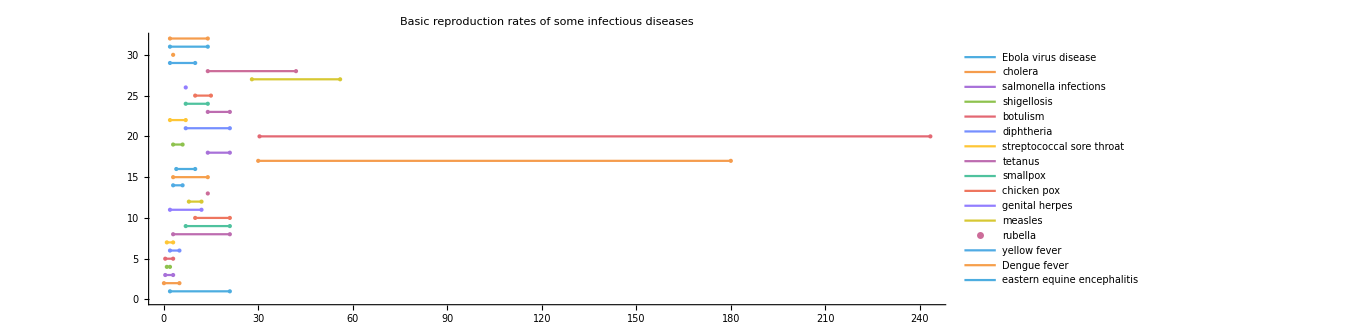

```mathematica
(* plot can be inproved with markers but NumberLinePlot doesn't support this option *)
Quiet@NumberLinePlot[List/@Values[infectDisExp], PlotLegends->Placed[Keys@infectDisExp, Below], PlotTheme->"Detailed", PlotStyle->110, ImageSize->{1000,Automatic}, AspectRatio->1/3, PlotLabel->"Basic reproduction rates of some infectious diseases", AxesLabel->{"Days"}]
```

```mathematica
(* TimelinePlot can't interpret time interval *)
TimelinePlot[Association@infectDisExp, ImageSize->1000, AspectRatio->1/GoldenRatio, PlotLayout->"Stacked", PlotLabel->"Exposure to disease onset time of some infectious diseases", PlotTheme->"Business"]
```

-Graphics-

```mathematica
(* reproduction no. (Subscript[R, 0]) of such diseases. note that data is not available for some entities  *)
infectDisR0 = DeleteMissing@ParallelMap[(# -> #[EntityProperty["Disease","BasicReproductionNumber"]])&, infectDis]
```

{Ebola virus disease→Interval[{1.5,2.5}],diphtheria→Interval[{6.,7.}],whooping cough→5.5,smallpox→Interval[{5.,7.}],measles→Interval[{12.,18.}],rubella→Interval[{5.,7.}],mumps→Interval[{4.,7.}],severe acute respiratory syndrome→Interval[{2.,5.}],influenza→Interval[{2.,3.}],Middle East respiratory syndrome→Interval[{0.6,1.}],COVID-19→Interval[{1.4,2.5}]}

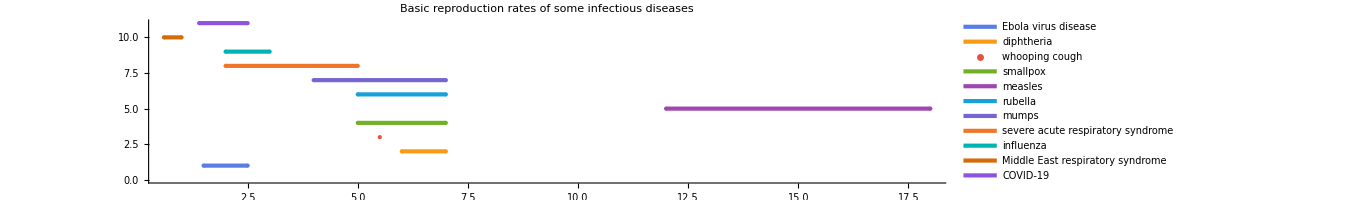

```mathematica
NumberLinePlot[Values@infectDisR0, PlotLegends->Placed[Keys@infectDisR0, Below], PlotTheme->"Business", ImageSize->{1000,Automatic}, AspectRatio->1/5, PlotLabel->"Basic reproduction rates of some infectious diseases"]
```